```mathematica
(*http://mathematica.stackexchange.com/questions/3242/can-mathematica-do-symbolic-linear-algebra*)
```

```mathematica
$Assumptions={Element[A,Matrices[{m,n}]],Element[B,Matrices[{n,k}]]};
TensorReduce[Transpose[Transpose[A].Transpose[B]]]
```

B.A

```mathematica
data = Table[{3 + i + RandomReal[{-3, 7}], i + RandomReal[{-2, 5}]}, {i, 1, 20}]
```

{{1.42803,2.35618},{8.37698,3.82602},{10.6925,1.70019},{4.4524,8.74668},{8.01996,9.98551},{10.9892,8.95594},{15.5748,10.2762},{15.1598,9.03631},{12.1994,13.0542},{12.8335,12.1403},{19.6651,14.3972},{18.4602,13.4512},{15.4846,15.6855},{23.7583,17.2794},{22.2652,17.2388},{17.2638,16.4095},{22.8517,19.641},{27.3888,16.4154},{23.4235,21.2765},{28.3234,23.0723}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[1.76765+0.689214 x]

```mathematica
model["BestFit"]
```

1.76765+0.689214 x

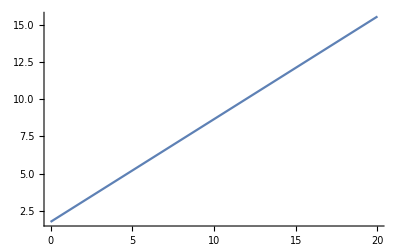

```mathematica
Plot[model["BestFit"], {x, 0, 20}]
```

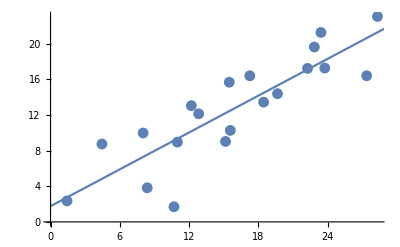

```mathematica
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 30}]]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.76765 | 1.6851 | 1.04899 | 0.308063
x | 0.689214 | 0.0962826 | 7.15824 | 1.14952×10^-6